# Ψ_1 proposal (penalizing function)

1/(1+ⅇ^(1/(-1+x)+1/x))

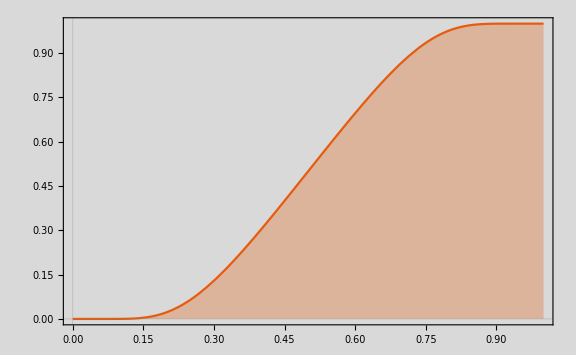

```mathematica
g[x_]=Exp[(-1/x)];
h[x_]=g[x]/(g[x]+g[1-x]) //FullSimplify
Plot[h[x],{x,0,1},ImageSize->Large,PlotTheme->"Scientific", Filling->Automatic, Background->LightGray,PlotRange->All]
```

Piecewise[{{0, x≤0}, {1/(1+ⅇ^(1/(-1+x)+1/x)), 0<x<1}, {1, 1≤x}, {0, True}}]

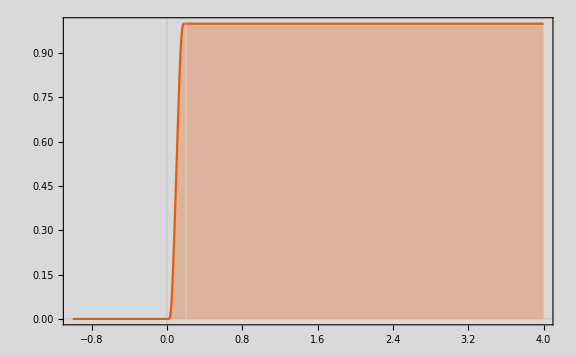

```mathematica
psi1[x_]=Piecewise[{{0,x<=0},{h[x],0<x<1},{1,1<=x}}]
Plot[psi1[5*x],{x,-1,4},ImageSize->Large,PlotTheme->"Scientific", Filling->Automatic, Background->LightGray,PlotRange->All]
```

```mathematica
psi1'[x]//FullSimplify
```

Piecewise[{{(2+4 (-1+x) x)/(4 (-1+x)^2 x^2 (1+Cosh[1/(-1+x)+1/x])), 0<x<1}, {0, True}}]

```mathematica
psi1''[x]//FullSimplify//Expand
```

Piecewise[{{(ⅇ^(1/(-1+x)+1/x) (-1+2 x-2 x^3 (2+x (-3+2 x))+ⅇ^(1/(-1+x)+1/x) (1-2 (-1+x) x (-3+2 x) (1+(-1+x) x))))/((1+ⅇ^(1/(-1+x)+1/x))^3 (-1+x)^4 x^4), 0<x<1}, {0, True}}]

# Ψ_2 proposal (smoothing function)

```mathematica
(*Perona-Malik regularizer*)
psi2[x_] = λ^2 Log[1. + x/λ^2]
psi2'[x] //FullSimplify
psi2''[x] //FullSimplify
```

λ^2 Log[1.+x/λ^2]

1/(1.+x/λ^2)

-(1. λ^2)/((x+1. λ^2)^2)

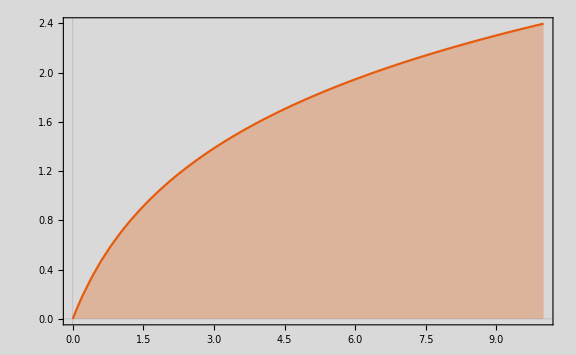

```mathematica
λ=1;
Plot[psi2[x],{x,0,10},ImageSize->Large,PlotTheme->"Scientific", Filling->Automatic, Background->LightGray,PlotRange->All]
```